# Adaptive Search for Structural Colors

Thanks for downloading this package! Depending on what you’re trying to do, different sub-packages will be of interest to you:

## General Start-Up

To use the package, open a new Mathematica notebook in the same location as the package, and evaluate these lines:

```mathematica
Get["StructuralColorFramework`",Path->NotebookDirectory[]]
```

This loads the general Structural Color package, which has two public functions:

```mathematica
?SpectrumToColor
```

```mathematica
?ColorToSpectrum
```

SpectrumToColor is the function underlying much of the calculations, and is added here independently for convenience.

ColorToSpectrum is used in case a sample reflectance spectrum is needed for debugging. It is the mathematical inverse of SpectrumToColor, and occasionally returns non-physical spectra.

#### Colors in Mathematica

Colors are visualized in Mathematica with the XYZColor function, which can be used to visually choose colors (start typing it out, and the option will appear).

```mathematica
XYZColor[0.27,0.26,0.74]
```

The Color object can be converted back into a set of XYZ coordinates with List@@:

```mathematica
List@@XYZColor[0.27, 0.26, 0.74]
```

#### Working with Spectra

```mathematica
blueSpectrum=ColorToSpectrum[List@@XYZColor[0.27, 0.26, 0.74]]
```

The Private`λ variable means that this result is coming from a package using a Private context.

```mathematica
Plot[blueSpectrum, {Private`λ, 385,745}]
```

```mathematica
XYZColor@SpectrumToColor[blueSpectrum]
```

In addition to the public functions, the StructuralColorFramework package includes many necessary private functions used by the 1D, 2D, and 3D sub-packages. They load it automatically.

## Design of 1D Stacks

```mathematica
Get["StructuralColor1D`",Path->NotebookDirectory[]]
```

This is the most simple of three sub-packages, but they all have a similar set of functions.

If you simply wish to know the spectrum or color of a certain photonic stack, use the Spectrum1D function:

```mathematica
?Spectrum1D
```

```mathematica
Spectrum1D[300,200,{1.49,1,5,0}]
```

```mathematica
XYZColor[SpectrumToColor[Spectrum1D[300,200,{1.49,1,5,0}]]]
```

This code was originally published via the Wolfram Demonstrations Project, http://demonstrations.wolfram.com/MultilayerPhotonicBandgap

#### Searching for a 1D Geometry

The “PhotonicSystemX” set of variables puts system parameters into the form used in the search.

```mathematica
?PhotonicSystem1D
```

In this case, the 1D search is designed to choose layer thicknesses when refractive indices and layer number are already chosen. This can be switched in the main code by adding layer thicknesses into the PhotonicSystem1D definition.

A 5-layer system with of PMMA and air, viewed from above, has the following entry:

```mathematica
PhotonicSystem1D[1.49, 1, 5, 0];
```

Now you’re ready to iterate! Just stick your desired color and the entire PhotonicSystem into the function Iteration1D

```mathematica
?Iteration1D
```

Use IterationReset1D if you want to stop searching for the same color.

```mathematica
?IterationReset1D
```

## Design of 2D Lattices (requires Fortran)

The 2D code is set up exactly like the 1D code, with one key difference: the calculations are performed with Fortran, so there’s a little more set-up involved.

The Fortran code was written by Ward and Pendry, and the original documentation is found here: http://www.cmth.ph.ic.ac.uk/photonics/Newphotonics/pdf/CompPCom128_590.pdf
The version of ONYX you downloaded has been modified, but the underlying calculation is the same.

The following instructions are for running the code using Terminal on a Mac. The set-up for a Windows machine should be very similar, but you’ll have to figure out the details on your own :)

You’ll need a Fortran compiler, available here: https://directory.fsf.org/wiki/Gfortran

This folder contains two .sh files, which are the file type read by the Terminal. If you save these files, the only thing you need to do in order to perform the 2D search is to run the Iteration2D function, and then run the Terminal files when asked to do so by Iteration2D (make sure your sound is on!).

IMPORTANT: open these files and change the file paths to wherever the ONYX files are stored on your computer. Unless you’re experienced at using Terminal, I recommend just storing them on your Home drive.

Now, go into the StructuralColor2D file, and change Users/emmavargo to wherever you have the rest of the ONYX files stored.

```mathematica
Get["StructuralColor2D`",Path->NotebookDirectory[]]
```

```mathematica
?PhotonicSystem2D
```

```mathematica
?Iteration2D
```

#### Searching for a 2D Geometry

The process is a little strange at first, so here’s step-by-step instructions:

Evaluate the following line:

```mathematica
Iteration2D[{.2,.3,.4},PhotonicSystem2D[1,3.4]]
```

You should have heard, “If you wish to keep searching, please run the Terminal file.” You then have 30 seconds to run the commands in Terminal before Mathematica starts looking for results.

To run the .sh files, type “sh “ into the Terminal and then drag the getOnyxDataset_[geometry].sh file into the Terminal window. The filepath should appear, and then you can just hit enter! Your geometry options are rect, for a rectangular lattice or hex, for a hexagonal lattice.

If the file runs correctly, you should see “Note: The following floating-point exceptions are signalling: IEEE_UNDERFLOW_FLAG IEEE_DENORMAL” appear in the Terminal window. It’s important to run Iteration2D before running the .sh file, because it creates a “MarkComplete” file the .sh talks to.

Each iteration will take about 10 minutes.

Your output will look like this:

These are the suggested dimensions:

{{8350,3653.13},{8300,3631.25},{8400,3675.},{8450,3644.06},{8500,3665.63},{8400,3622.5},{8550,3633.75},{8600,3655.},{8500,3612.5},{8250,3609.38}}

These are the corresponding colors:

{XYZColor[{0.22379864127802554, 0.3106325678220307, 0.34437671115387486}],XYZColor[{0.21557278567261576, 0.30407396582166163, 0.33365527901694225}],XYZColor[{0.23287969475812503, 0.3165684292671393, 0.35391167938734897}],XYZColor[{0.2171169487534784, 0.30411907773179847, 0.3332697150053751}],XYZColor[{0.22467813097484018, 0.310272680697447, 0.3411043707152691}],XYZColor[{0.21055157042644262, 0.297472942710339, 0.324602048633836}],XYZColor[{0.21113921391521742, 0.2963323608142429, 0.3233694881816569}],XYZColor[{0.21774835752343283, 0.3023614843232243, 0.32959209982611753}],XYZColor[{0.20554202224483023, 0.2898748229212522, 0.31644061282765834}],XYZColor[{0.20841348710304464, 0.2970079242089155, 0.3221337242165446}]}

These are the color distances in the CIELAB colorspace:

{0.0483746,0.0499385,0.0500852,0.0506535,0.050995,0.0519475,0.0524035,0.0528491,0.0531675,0.0535341}

The best match has a lattice constant of 8350 nm with a hole radius of 3653.13 nm.
Here is the color of this match (right) compared to your desired color (left):

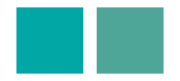

This has a color distance of 0.0483746 . If you want to keep iterating evaluate the Iteration2D function again.

Evaluate the same function again if you want to keep searching.

## Design of 3D Glasses

The 3D code runs exactly like the 1D code, so no sweat!

The code for this calculation was originally written in Python by the Manoharan Group. Their code can be found here: https://github.com/manoharan-lab/structural-color
The translated Mathematica code is found as part of the StructuralColor3D package.

```mathematica
Get["StructuralColor3D`",Path->NotebookDirectory[]]
```

```mathematica
?PhotonicSystemGlass
```

```mathematica
?Iteration3D
```

As of now, the matrix material must have a lower refractive index than the particle material.

```mathematica
Iteration3D[{0.2,0.4,0.3}, PhotonicSystemGlass[1.49,1.]]
```

Each iteration should take a couple of minutes.

As before, use IterationReset3D if you want to switch to a new color

```mathematica
?IterationReset3D
```

## Design of a New Geometry (make your own!)

If you’d like to design for a completely new geometry, all you need is code that will output a reflectance spectrum given a set of parameters. It’s easiest if this code is written in Mathematica, and it’s often worth your time to translate into Mathematica from another language if the code is short enough. If you don’t want to translate, look at the 2D sub-package for an example of interfacing with an external compiler.

The StructuralColorTemplate sub-package is meant to guide you through the process of making your own sub-package. Open it! (It may be useful to open StructuralColor1D as well as a reference.)

## Using an Image as a Template

The notebook “Design_From_An_Image” will walk you through the process.